Last modified on: Wednesday, July 11, 2018 at 12:10

Author Info

Thiago  R. Bergamaschi

Matthew  Szudzik

Massachusetts  Institute  of  Technology

Poster Session Content

Optimal Packing of Bidisperse Circles

The goal  of this project is to simulate  and study  approximate  optimal packing of many 2D disks of 2 different radii, through  an Event-Driven Lubachevsky-Stillinger  algorithm.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

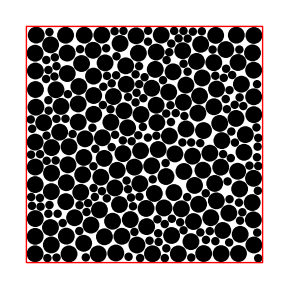
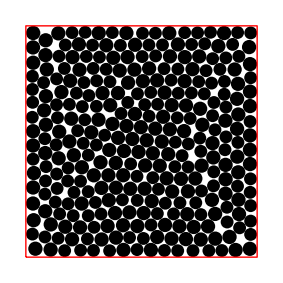

Implementation  of the ED LS algorithm,  and simulation  of various approximate  jammed packs.
Implementation  of an Augmented Min-Heap data structure  and design of an amortized  O(log n) extractmin operation.
-Graphics--Graphics-

Analysis  and  investigation  of the simulated  packs, including studying pair correlation  functions. 
Further tuning precision and efficiency of the algorithm  implementation  in Mathematica.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Simulation Results

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

# ED LSA Development

Here are the functions I wrote for this project. The code is based on the C++ implementation of the algorithm in the first reference below. A full algorithmic description can be found there, but documentation and function explanations follow the function definitions below.

The algorithm is based on an event-driven process, where after any particle performs an event, its next event is calculated and reinserted into the data structure. All events will be denoted by triples e={te, i, p}. te denotes the time of the event, i the particle index, and p, the event partner. p can be another particle, if 1≤p≤N, and thus the event is a collision, or a transfer, i.e., the particle is traversing a cell wall, if N+1≤p≤N+4. p-N indicates the wall index, where 1 is the right wall, 2 the left, 3 the top, and 4 the bottom.

## Constraints

Constraint functions to test particle position validity. Returns booleans.

### overlapC

Returns True if circles don’t overlap, False o.w. Local variables only.

#### Definitions

```mathematica
overlapC[{{x1_, y1_}, r1_}, {{x2_, y2_}, r2_}]:=
((r2+r1)^2≤(y2-y1)^2+(x2-x1)^2)
```

#### Testing

```mathematica
overlapC[{{1,1},1}, {{0,0},.5}]
```

False

### borderC

Returns True if in square region, False o.w.

#### Definitions

```mathematica
borderC[{x_, y_}, r_]:=And[
size-r≥x, size-r≥y,r≤x, r≤y
]
```

#### Testing

```mathematica
borderC[{1,1},1, 2]
```

True

### overlapQ

#### Definition

```mathematica
overlapQ:=And@@(Table[overlapC[{positions⟦i⟧, radii⟦i⟧}, {positions⟦j⟧, radii⟦j⟧}], {i, 1, n}, {j, i+1, n}]//Flatten)
```

#### Testing

```mathematica
Table[overlapC[{positions⟦i⟧, radii⟦i⟧}, {positions⟦j⟧, radii⟦j⟧}], {i, 1, n},{j, 1+i, n}]//Flatten
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
overlapQ
```

Part::pkspec1: The expression j cannot be used as a part specification.

Table::iterb: Iterator {positions⟦j⟧,{0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,«39»,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,«50»}⟦j⟧} does not have appropriate bounds.

Table[{positions⟦i⟧,radii⟦i⟧},{positions⟦j⟧,{0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.0223607,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427,0.00894427}⟦j⟧},{i,1,n},{j,i+1,n}]

## Initialization

### rlist

This function initializes all radii at small values satisfying minimum packing fraction.

#### Definition

```mathematica
ClearAll[rlist]
```

```mathematica
rlist[minpf_, size_, n_, bratio_ , rratio_]:=Block[{a, r, t1, t2},
a=size^2 minpf/(4 n);
r=a//Sqrt;
t1=Table[r, Floor[n bratio]];
t2=Table[r rratio, Ceiling[n (1- bratio)]];
Join[t1, t2]
]
```

#### Testing

```mathematica
rlist[.01, 1, 10, .2, .4]
```

{0.0316228,0.0316228,0.0126491,0.0126491,0.0126491,0.0126491,0.0126491,0.0126491,0.0126491,0.0126491}

### createDisk

Randomly generates disk coordinates that satisfy constraints above. Takes list of current circle positions, set of all radii and boundary size. Returns coordinate that satisfies such.

#### Definition

```mathematica
createDisk[circles_List,radii_List, size_]:=Module[
{cnumber=circles//Length, position, riffled, count=0, insert=False, rc, r},

(*splice radii list, select next*)
rc=radii⟦;;cnumber⟧;
r=radii⟦cnumber+1⟧;
riffled=Riffle[circles,rc]//Partition[#, 2]&;

(*testing loop*)
While[
(*stop when inserted or overcount*)
And[count<100, !insert ],
	position=RandomReal[{0, size}, 2];

(*if doesn't overlap border or overlap other circle*)
	
	If[And[
	borderC[position,r],
	And@@(overlapC[{position, r}, #]&/@riffled)
	],
	insert=True;
	];
count=count+1;
];
If[count==200, Print["fail"]];

position
]
```

#### testing

```mathematica
createDisk[{{1,1}, {2,2}}, {.5,.4, 1}, 7]
```

{4.95242,3.36112}

### createDisks

Randomly generates initial coordinates for the set of radii. Returns list of coordinate tuples.

#### Definitions

```mathematica
createDisks[radii_List, size_]:=Module[
{coordinates, number=radii//Length},
coordinates={createDisk[{}, radii, size]};
Nest[Join[#,{createDisk[#, radii, size]}]&, coordinates, number-1]
]
```

#### testing

```mathematica
rlist={1,1,1,.5,.5,.5,.5}
```

{1,1,1,0.5,0.5,0.5,0.5}

```mathematica
c=createDisks[{1,1,1,.5,.5,.5,.5}, 10]
```

{{7.8944,7.54713},{1.42687,5.23831},{4.47153,5.10797},{3.78713,8.13987},{0.77426,0.585312},{2.78468,2.74413},{7.79009,4.36008}}

```mathematica
displayParticles[%, {1,1,1,.5,.5,.5,.5}]
```

displayParticles[{{7.8944,7.54713},{1.42687,5.23831},{4.47153,5.10797},{3.78713,8.13987},{0.77426,0.585312},{2.78468,2.74413},{7.79009,4.36008}},{1,1,1,0.5,0.5,0.5,0.5}]

Doesn’t Overlap!

### velocityInit

Randomly initializes velocities. Function subject to modification with final implementation. Returns list of tuples.

#### Definitions

```mathematica
velocityInit[size_,number_]:=RandomReal[size{-1, 1}, {number,2}]
```

#### Testing

```mathematica
velocityInit[4,5]
```

{{-0.818614,0.0337972},{0.0032856,-0.507769},{0.914631,-0.109944},{0.68358,0.881663},{-0.790859,0.142455}}

### setInitialEvents

Initializes all events to checks, initializes heap and hash to blank check events and map.

#### Definitions

```mathematica
setInitialEvents[n_, gtime_:0]:=(
nextevents = Table[{gtime, i, Infinity}, {i, n}];
{heap, hash} = hInitialize[n];
)
```

#### Testing

```mathematica
setInitialEvents[10]
```

```mathematica
hash
heap
nextevents
```

<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>

{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10}}

{{0,1,∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

## Cell Method

### optimalGrid

Takes maximum radius, returns optimal number of grid rows.

#### Definition

```mathematica
optimalGrid[size_,currentradius_]:=Ceiling@( size/(2 currentradius))
```

#### Testing

```mathematica
optimalGrid[10, 1]
```

5

### binCenters

Defines nrows^2 center coordinates. Returns matrix of coordinates - list of lists of tuples.

#### Definition

```mathematica
binCenters[nrows_, size_]:=With[{step=size/nrows},
Table[step{i, j}/2, {i, 1, 2nrows,2}, {j, 1, 2nrows,2}]
]
```

#### Testing

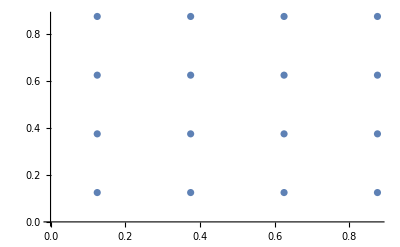

```mathematica
binCenters[4,1 ]//Flatten//Partition[#,2]&//ListPlot
```

### nearestCells

Maps list of coordinates to matrix of bins by index. Returns cellMatrix, a list of lists (bins) with index numbers representing the particle centers in the specific cell.

#### Definition

```mathematica
nearestCells[coordinates_, nrows_, size_]:=Module[
{nf=Nearest[coordinates->Range@Length@coordinates, DistanceFunction->ChessboardDistance], coordinatemat},
nf[binCenters[nrows, size], {Infinity, size/(2 nrows)}]
]
```

#### Testing

```mathematica
Clear[data, cellMatrix]
```

```mathematica
data=RandomReal[10, {50, 2}];
```

```mathematica
cellMatrix=nearestCells[data, 4, 10]
```

{{{},{33,8},{4,1,28},{12,38,21}},{{13,3,39,30},{18,14},{11,48,7,35,49},{36,44}},{{43,9},{16},{25,31,40,45,42,29},{41,24,22,23,5}},{{46,32,34},{15,10},{37,17,50,47},{19,20,26,2,6,27}}}

```mathematica
Association[Flatten[MapIndexed[Function[{list,pos},#->pos&/@list],cellMatrix,{2}]]]
```

<|33→{1,2},8→{1,2},4→{1,3},1→{1,3},28→{1,3},12→{1,4},38→{1,4},21→{1,4},13→{2,1},3→{2,1},39→{2,1},30→{2,1},18→{2,2},14→{2,2},11→{2,3},48→{2,3},7→{2,3},35→{2,3},49→{2,3},36→{2,4},44→{2,4},43→{3,1},9→{3,1},16→{3,2},25→{3,3},31→{3,3},40→{3,3},45→{3,3},42→{3,3},29→{3,3},41→{3,4},24→{3,4},22→{3,4},23→{3,4},5→{3,4},46→{4,1},32→{4,1},34→{4,1},15→{4,2},10→{4,2},37→{4,3},17→{4,3},50→{4,3},47→{4,3},19→{4,4},20→{4,4},26→{4,4},2→{4,4},6→{4,4},27→{4,4}|>

```mathematica
binCenters[4,10];
```

```mathematica
m
```

{{{40,2,29},{9,36,16},{33,41},{50}},{{1,43,44,4,27},{31,32},{12,28,23},{15,20,49,35,8}},{{14},{22,42,11},{47,38,18},{5,19,3,30,45,6,48}},{{34,39,10},{21,25,26},{17},{7,24,13,46,37}}}

```mathematica
m
```

{{{40,2,29},{9,36,16},{33,41},{50}},{{1,43,44,4,27},{31,32},{12,28,23},{15,20,49,35,8}},{{14},{22,42,11},{47,38,18},{5,19,3,30,45,6,48}},{{34,39,10},{21,25,26},{17},{7,24,13,46,37}}}

{{{},{{0.805173,3.31452},{0.883983,4.40272},{1.65688,4.40467},{1.96505,3.78695}},{{1.806,6.42057},{2.14145,6.03385}},{{0.65088,8.88589},{0.797013,9.64187}}},{{{3.97731,1.4623},{3.0372,1.25763},{4.48522,1.07146},{4.64892,1.99548}},{{3.75446,3.25761},{4.50227,2.76267}},{{3.62191,5.63893},{4.46167,6.02467},{3.27454,7.01114}},{{3.79164,8.58965}}},{{{5.37395,0.752036},{5.8744,0.284669}},{},{{6.5581,5.46856},{7.15174,6.77586},{7.1897,5.49383}},{{6.92188,9.30649}}},{{{8.30408,1.48281},{8.74998,0.340356}},{{8.62647,3.73118},{8.36794,4.24888},{9.57911,3.66747},{9.42693,4.64879}},{{8.77438,6.21068},{8.0161,6.8461},{9.68578,6.45644}},{{9.45638,8.76425}}}}

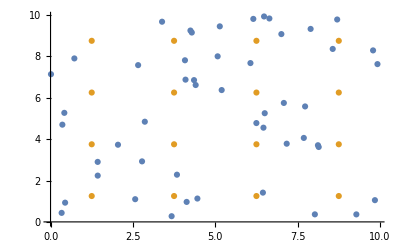

```mathematica
ListPlot[{data, binCenters[4, 10]//Flatten[#, 1]&}]
```

### cellMap

Maps disk coordinate to bin. Returns binindex tuple.

#### Definition

```mathematica
ClearAll[cellMap]
```

```mathematica
cellMap[coordinate_]:=With[{step=size/nrows},
Ceiling[(coordinate)/step]
]
```

#### Testing

Note that particles won’t overlap boundary, so no edge cases.

```mathematica
cellMap[{0,2}, 5, 9]
```

{0,4}

### cellAssociation

This function will invert cellMatrix into a association, where each index i maps to the current cell corresponding to coordinate i.

#### Definition

```mathematica
cellAssociation[cellMatrix_]:= Association[Flatten[
MapIndexed[Function[{list, pos}, # ->pos &/@list],
cellMatrix,
{2}]]];
```

#### Testing

```mathematica
Clear[data, cellMatrix, cellA]
```

```mathematica
data=RandomReal[10, {50, 2}];
cellMatrix=nearestCells[data, 4, 10];
cellA=cellAssociation[cellMatrix]
```

<|15→{1,2},13→{1,2},43→{1,3},50→{1,3},47→{1,3},10→{1,3},30→{1,4},11→{1,4},46→{2,1},5→{2,2},20→{2,2},4→{2,2},33→{2,2},45→{2,3},26→{2,3},35→{2,3},2→{2,3},8→{2,4},17→{2,4},3→{2,4},29→{2,4},28→{2,4},40→{3,1},48→{3,1},36→{3,1},38→{3,1},41→{3,1},7→{3,1},39→{3,1},24→{3,2},44→{3,2},19→{3,2},23→{3,2},31→{3,3},49→{3,3},32→{4,1},12→{4,1},16→{4,1},21→{4,1},25→{4,1},6→{4,2},1→{4,2},34→{4,2},14→{4,2},37→{4,3},22→{4,3},18→{4,4},9→{4,4},27→{4,4},42→{4,4}|>

```mathematica
cellA[1]
```

{4,2}

```mathematica
(*note: means nothing*)
cellA⟦1⟧
```

{1,2}

### findNeighbors

Returns list of indices, corresponding to possible collision pairs. Defined through maximum of 8 neighboring cells, as well as current cells. Note that includes itself.

#### Definition

```mathematica
findNeighbors[coordinate_]:=Module[
{i, j, currentlist, cl, ck, l, k,cellindex},
cellindex = cellMap[coordinate];
(*particle cell & initialization*)
{i, j}=cellindex;
currentlist={};
(*iteration through cells, eliminating edge cases*)
For[k=-2, k<3, k++,
ck=cellindex⟦1⟧+k;
If[ck≤ nrows && ck≥1,
For[l=-2, l<3, l++,
cl=cellindex⟦2⟧+l;
If[cl≤ nrows && cl≥1,
currentlist=Join[currentlist, cellMatrix⟦ck, cl⟧];
]]]];
currentlist
]
```

#### Testing

```mathematica
Clear[data, cellMatrix, cellA]
```

```mathematica
data=RandomReal[10, {50, 2}];
cellMatrix=nearestCells[data, 4, 10];
cellA=cellAssociation[cellMatrix];
cellA[1]
```

{2,1}

```mathematica
findNeighbors[cellMatrix, cellA⟦1⟧, 4]//Length
```

13

### updateCell

Function modifies in place cellA and cellMatrix, updating particle i’s index and association map. Takes index and new cell indices. Returns nothing.

#### Definition

```mathematica
updateCell=Function[{i, newcell},
Module[
{currentk, currentj, oldk, oldj},
(*initialize variables*)
{currentk, currentj}=newcell;
{oldk, oldj}=cellA[i];
(*delete and reinsert element from cellMat*)
cellMatrix⟦oldk, oldj⟧=Select[cellMatrix⟦oldk, oldj⟧, #≠i&];
AppendTo[cellMatrix⟦currentk, currentj⟧, i];
(*reset element in association*)
cellA[i]={currentk, currentj};
],
HoldAll
];
```

#### Definition2

Previous version, in place with holdall.

```mathematica
updateCell2=Function[{i, coordinates, cellA, cellMat, size, nrows},
Module[
{currentk, currentj, oldk, oldj},
(*initialize variables*)
{currentk, currentj}=cellMap[coordinates⟦i⟧, size, nrows];
{oldk, oldj}=cellA[i];
(*delete and reinsert element from cellMat*)
cellMat⟦oldk, oldj⟧=Select[cellMat⟦oldk, oldj⟧, #≠i&];
AppendTo[cellMat⟦currentk, currentj⟧, {i}];
(*reset element in association*)
cellA[i]={currentk, currentj};
],
HoldAll
];
```

#### Testing

```mathematica
coordinates=RandomReal[10, {50, 2}];
cellMatrix=nearestCells[coordinates, 4, 10];
cellA=cellAssociation[cellMatrix];
cellA[1]
```

{4,1}

```mathematica
cellMatrix⟦%⟦1⟧, %⟦2⟧⟧
```

{1,23,31,49,48,24}

```mathematica
coordinates⟦1⟧={9,9};
```

```mathematica
updateCell[1, cellMap[coordinates⟦1⟧, 10, 4]]
cellA[1]
```

{4,4}

```mathematica
cellMatrix⟦%⟦1⟧, %⟦2⟧⟧
```

{27,15,25,20,1}

Cell of 1 has updated!

### changeBins

This function will reset the global variables cellMatrix and cellA, resetting the bins. It’s input is just the new number of rows nrows, and it requires the global variables positions and size.

#### Definition

```mathematica
changeBins[nrows_] := Block[{},
 cellMatrix=nearestCells[positions, nrows, size];
 cellA = cellAssociation[cellMatrix];
]
```

#### Testing

```mathematica
Clear[size, positions]
```

```mathematica
size = 10;
positions=RandomReal[size, {5, 2}];
```

```mathematica
changeBins[4]
```

```mathematica
cellMatrix
cellA
```

{{{},{2,4},{},{}},{{},{},{5},{}},{{},{},{},{}},{{3},{},{1},{}}}

<|2→{1,2},4→{1,2},5→{2,3},3→{4,1},1→{4,3}|>

## Augmented Min Heap Implementation

I will implement a min-Heap using a list heap. The Heap will store tuples {t, i}, where t is the time of the next collision including particle i. This will support insert and extract_min operations in O(log n) operations. On top of it, I’ll implement a hash table (association) hash that will map each particle index to heap position.
This will support lookup operations in O(1).

### hInitialize

This function will output a blank heap of size n, and a association mapping heap index to particle index (initially).

#### Definition

```mathematica
hInitialize[n_]:=Block[{heap, hash},
	heap = Table[{0, i}, {i, n}];
	hash = Association[Table[i->i, {i,n}]];
	{heap, hash}
]
```

#### Testing

```mathematica
{heap, hash}=hInitialize[10];
```

```mathematica
hash[1]
```

1

```mathematica
heap⟦1⟧
```

{0,1}

### HeapQ

Tests if heap  is a min-Heap in O(N). Recall that heap is a list of tuples, not of Reals.

#### Definition

```mathematica
HeapQ[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧⟦1⟧≤ a⟦i⟧⟦1⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a = Table[{0,i}, {i, 10}];
```

```mathematica
HeapQ[a]
```

True

```mathematica
a=RandomReal[1, {10, 2}];
a//HeapQ
```

False

### hSwap

Function swaps elements i and j of heap.

#### Definition

```mathematica
hSwap[i_,j_]:=Block[{},
	{heap⟦i⟧, heap⟦j⟧}={heap⟦j⟧, heap⟦i⟧};
	{hash[heap⟦i⟧⟦2⟧], hash[heap⟦j⟧⟦2⟧]}={hash[heap⟦j⟧⟦2⟧], hash[heap⟦i⟧⟦2⟧]};
	]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
hSwap[1,2]
heap
hash
```

{{0.311443,2},{0.0874412,1},{0.367118,3},{0.393195,4},{0.462672,5},{0.470538,6},{0.545019,7},{0.58925,8},{0.636436,9},{0.699941,10}}

<|1→2,2→1,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>

### hashify

Hashes particle index to position in heap list.

#### Definitions

```mathematica
hashify[heap_]:=AssociationThread[heap⟦All, 2⟧,Range[heap//Length]]
```

#### Testing

```mathematica
Clear[l, heap, hash]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10, 1, -1]]//Partition[#, 2]&;
```

```mathematica
heap
```

{{0.0411028,10},{0.227518,9},{0.29996,8},{0.385275,7},{0.413419,6},{0.694847,5},{0.853615,4},{0.854638,3},{0.897921,2},{0.949822,1}}

```mathematica
hashify[heap]
```

<|10→1,9→2,8→3,7→4,6→5,5→6,4→7,3→8,2→9,1→10|>

### HeapifyDown

Recursively updates heap and hash downwards, following minHeap property. Takes index in heap, not particle index!

#### Definition

```mathematica
HeapifyDown[i_]:=Module[
{ n = heap//Length},
Which[ 
	n < 2i,
	heap;,
	(*at leaf*)
	n ≤ 2i && heap⟦i⟧⟦1⟧ ≥ heap⟦2i⟧⟦1⟧, 
	hSwap[i, 2i];
	HeapifyDown[2i];,
	(*only left child*)
	n ≤ 2i && heap⟦i⟧⟦1⟧ ≤  heap⟦2i⟧⟦1⟧, 
	heap,
	(*only left child, satisfied*)
	heap⟦i⟧⟦1⟧ ≤ heap⟦2i⟧⟦1⟧ && heap⟦i⟧⟦1⟧ ≤ heap⟦2i+1⟧⟦1⟧, 
	heap;,
	(*property satisfied*)
	heap⟦i⟧⟦1⟧ ≥ Min[heap⟦2i⟧⟦1⟧, heap⟦2i+1⟧⟦1⟧] && heap⟦2i⟧⟦1⟧ ≤ heap⟦2i+1⟧⟦1⟧,
	hSwap[i, 2i];
	HeapifyDown[2i];,
	(*swap with left child*)
	heap⟦i⟧⟦1⟧≥  Min[heap⟦2i⟧⟦1⟧, heap⟦2i+1⟧⟦1⟧] && heap⟦2i⟧⟦1⟧ > heap⟦2i+1⟧⟦1⟧,
	hSwap[i, 2i+1];
	HeapifyDown[2i+1];
	(*swap with right child*)
 ]
];
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
heap⟦1⟧⟦1⟧=1;
```

```mathematica
HeapifyDown[1]
heap
hash
```

{{0.156983,2},{0.296438,4},{0.209844,3},{0.509609,8},{0.33106,5},{0.354964,6},{0.397934,7},{1,1},{0.533739,9},{0.585573,10}}

<|1→2,2→4,3→3,4→8,5→5,6→6,7→7,8→1,9→9,10→10|>

```mathematica
heap//HeapQ
```

True

### HeapifyUp

Recursively updates heap and hash upwards, following minHeap property.

#### Definition

```mathematica
HeapifyUp[i_]:= Module[
	{n = heap//Length},
	Which[
		i==1,
		heap;,
		(*at root*)
		heap⟦i⟧⟦1⟧ ≥ heap⟦Floor[i/2]⟧⟦1⟧,
		heap;,
		(*satisfies minHeap prop, return*)
		heap⟦i⟧⟦1⟧≤ heap⟦Floor[i/2]⟧⟦1⟧,
		hSwap[i, Floor[i/2]];
		HeapifyUp[Floor[i/2]];
		(*swap with parent, if greater*)
	];
]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
heap⟦10⟧⟦1⟧=.1;
```

```mathematica
HeapifyUp[10];
heap
hash
```

{{0.0194323,1},{0.1,10},{0.429523,3},{0.436619,4},{0.254338,2},{0.600514,6},{0.855869,7},{0.895518,8},{0.919224,9},{0.484514,5}}

<|1→1,2→10,3→3,4→4,5→2,6→6,7→7,8→8,9→9,10→5|>

```mathematica
heap//HeapQ
```

True

### increaseKey

Increases key of particle i to newkey, applies heapifydown.

#### Definition

```mathematica
increaseKey[i_, newkey_]:=Block[
{index = hash[i]},
heap⟦index⟧⟦1⟧ = newkey;
HeapifyDown[index];
]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=hashify[heap];
```

```mathematica
heap
```

{{0.0235536,1},{0.256778,2},{0.304374,3},{0.350629,4},{0.555817,5},{0.658874,6},{0.849411,7},{0.854131,8},{0.86699,9},{0.967345,10}}

```mathematica
increaseKey[1, .9]
```

```mathematica
heap
```

{{0.256778,2},{0.350629,4},{0.304374,3},{0.854131,8},{0.555817,5},{0.658874,6},{0.849411,7},{0.9,1},{0.86699,9},{0.967345,10}}

### decreaseKey

Decreases key of particle i to newkey, applies heapifyup.

#### Definition

```mathematica
decreaseKey[i_, newkey_]:=Block[
{index = hash[i]},
heap⟦index⟧⟦1⟧ = newkey;
HeapifyUp[index];
]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=hashify[heap];
```

```mathematica
heap
```

{{0.0324041,1},{0.0444185,2},{0.0512898,3},{0.132947,4},{0.416869,5},{0.549748,6},{0.657425,7},{0.751741,8},{0.915551,9},{0.962497,10}}

```mathematica
decreaseKey[10, .1]
```

```mathematica
heap
```

{{0.0324041,1},{0.0444185,2},{0.0512898,3},{0.132947,4},{0.1,10},{0.549748,6},{0.657425,7},{0.751741,8},{0.915551,9},{0.416869,5}}

### buildH

Function builds heap in O(N). n is length of list

#### Definitions

```mathematica
buildH[n_]:=Map[HeapifyDown[#]&, Range[Floor[n/2], 1, -1]];
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10];
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=hashify[heap];
```

```mathematica
heap
```

{{0.307459,1},{0.261054,2},{0.254827,3},{0.479103,4},{0.367757,5},{0.0794808,6},{0.830831,7},{0.836803,8},{0.912273,9},{0.973477,10}}

```mathematica
buildH[10];
```

```mathematica
heap
```

{{0.0794808,6},{0.261054,2},{0.254827,3},{0.479103,4},{0.367757,5},{0.307459,1},{0.830831,7},{0.836803,8},{0.912273,9},{0.973477,10}}

```mathematica
heap//HeapQ
```

True

```mathematica
hash
```

<|1→6,2→2,3→3,4→4,5→5,6→1,7→7,8→8,9→9,10→10|>

### hInsert

This function appends the element to the end of the heap, and places it with HeapifyUp.

#### Definition

```mathematica
hInsert[element_]:= Block[
	{i, n = 1 + (heap//Length)},
	i = element⟦2⟧;
	AppendTo[heap, element];
	hash[i] = n;
	HeapifyUp[n];
	]
```

#### Testing

```mathematica
Clear[heap, hash, l, element]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
element={.21, 11};
```

```mathematica
hInsert[element]
```

```mathematica
heap
hash
```

{{0.0378967,1},{0.21,11},{0.252934,3},{0.255991,4},{0.243043,2},{0.400869,6},{0.439877,7},{0.671468,8},{0.689713,9},{0.985999,10},{0.326135,5}}

<|1→1,2→11,3→3,4→4,5→2,6→6,7→7,8→8,9→9,10→10,11→5|>

```mathematica
heap//HeapQ
```

True

### extractMin

This function returns the minimum element in amortized O(log n) time.

#### Definition

```mathematica
extractMin[particlenumber_]:= Module[
{minevent, index, n},

(*initialize variables*)
minevent = heap⟦1⟧;
index = minevent⟦2⟧;
n = heap//Length;

(*swap min with last*)
hSwap[1, n];

(*divide into amortization cases*)
If[ecounter < particlenumber,

	ecounter = ecounter + 1;

	(*drop particle index, hash null element*)
	hash[index]=.;
	hash[particlenumber+ecounter]=n;
	heap⟦n⟧={Infinity, particlenumber+ecounter};
	Print[ecounter];
	,

	(*drop particle index, set to null element*)
	hash[index]=.;
	heap⟦n⟧ = {Infinity, index};
	
	(*amortization step*)
	ecounter = 0;
	heap = Select[heap, #⟦1⟧≠Infinity&];
	hash = hashify[heap];

	buildH[heap//Length];
];
Print[hash, heap];

(*correct top element*)
HeapifyDown[1];

(*extract min*)
minevent
];
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
ecounter = 10;
l = RandomReal[1, 10]//Sort;
j = Table[{Infinity, i}, {i, 11, 20}];
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
heap=Join[heap, j]
hash=hashify[heap]
```

{{0.138601,1},{0.161965,2},{0.174238,3},{0.287829,4},{0.343459,5},{0.51577,6},{0.525993,7},{0.718666,8},{0.823038,9},{0.995475,10},{∞,11},{∞,12},{∞,13},{∞,14},{∞,15},{∞,16},{∞,17},{∞,18},{∞,19},{∞,20}}

<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10,11→11,12→12,13→13,14→14,15→15,16→16,17→17,18→18,19→19,20→20|>

```mathematica
extractMin[10]
```

<|2→1,3→2,4→3,5→4,6→5,7→6,8→7,9→8,10→9|>{{0.161965,2},{0.174238,3},{0.287829,4},{0.343459,5},{0.51577,6},{0.525993,7},{0.718666,8},{0.823038,9},{0.995475,10}}

{0.138601,1}

```mathematica
hash
heap
```

<|7→1,8→2,9→4,10→8,11→6,12→9,13→5,14→7,15→3,16→10|>

{{0.458374,7},{0.560385,8},{∞,15},{0.834321,9},{∞,13},{∞,11},{∞,14},{0.966979,10},{∞,12},{∞,16}}

```mathematica
a=<|"a"->1|>
```

<|a→1|>

```mathematica
a["a"]=.
```

```mathematica
a
```

<||>

### obtainMin

#### Definition

```mathematica
obtainMin[heap_]:=heap⟦1⟧;
```

#### Testing

```mathematica
Clear[heap]
```

```mathematica
heap=RandomReal[10,10]//Sort;
obtainMin@heap
```

0.156408

## Collisions

These are functions that will calculate the next collision event, and process current collision events.

### calculateCollision

Calculates time until collision between particles i and j, starting at gtime. If they don’t collide, return infinity. Takes indices i and j of variables, needs global variables radii, positions, velocities, lastupdates, rate and gtime.

#### Definition

```mathematica
calculateCollision[i_, j_]:= Module[
{nRi, nRj, d, σ, ΔR, ΔV, A, B, C, t},
(*sets positions and radii to current time*)
nRi=positions⟦i⟧+(gtime-lastupdates⟦i⟧)velocities⟦i⟧;
nRj=positions⟦j⟧+(gtime-lastupdates⟦j⟧)velocities⟦j⟧;
σ=(radii⟦i⟧+radii⟦j⟧)^2;

(*define helper variables*)
ΔR=nRi-nRj;
ΔV=velocities⟦i⟧-velocities⟦j⟧;
A=ΔV.ΔV-rate^2 σ;
B=ΔV.ΔR-rate(1+rate gtime)σ;
C=ΔR.ΔR-σ(1+rate gtime)^2;
d=B^2-A C;

(*debugging tests*)
If[C<-10^(-2)(radii⟦i⟧+radii⟦j⟧)(1+gtime rate), Print["After ", totalevents, " events, overlap."]; Abort[]];

(*calculate time*)
Which[
	C <-10^(-4)(radii⟦i⟧+radii⟦j⟧)(1+gtime rate) && B < 0, Print["spheres are already overlapping ", C]; Infinity,
	
	 d ≤ 0, Infinity,  
		
	True, -(B+Sqrt[d])/(A)
	]
]
```

#### Testing

```mathematica
Clear[positions, velocities, lastupdates, gtime, rate, radii]
```

```mathematica
positions=RandomReal[10, {10, 2}];
positions⟦1⟧=-{1,1};
positions⟦2⟧={1,1};
velocities=RandomReal[{-1, 1}, {10, 2}];
velocities⟦1⟧={1,1};
velocities⟦2⟧=-{1,1};
lastupdates=Table[1, 10];
gtime=1.1;
rate=1;
radii={.5, .5};
```

```mathematica
calculateCollision[1,2]
```

0.26115

### predictCollision

#### Development

```mathematica
predictCollision[i_, j_]:=Block[{ctime = calculateCollision[i, j]},
If[(ctime + gtime < nextevents⟦j⟧⟦1⟧) && (ctime > 0), ctime, Infinity]
];
```

### findNextCollision

Function returns collision event. Calculates time for all possible collision pairs following cell Method. Requires global variables cellMatrix, positions, size, nrows, plus global variables of dependent functions.

#### Definition

```mathematica
ClearAll[findNeighbors]
```

```mathematica
findNextCollision[i_] := Module[
{neighbors, times, cpair, mintime, coordinate},

(*define current position of particle i*)
coordinate = positions⟦i⟧+velocities⟦i⟧(gtime - lastupdates⟦i⟧);

(*find neighbors, calculate minimum collision times*)
neighbors = Select[findNeighbors[coordinate], #≠i&];
times = predictCollision[i, #]&/@neighbors;

(*obtain minimum*)
mintime = Min[times];

(*filter out no collisions -> infinity*)
If[
 (Select[times, (# ≠ Infinity)&]//Length)!=0,
	cpair = neighbors⟦Ordering[times]⟦1⟧⟧;,
	cpair = Infinity;
];

(*return collision event*)
{mintime+gtime, i, cpair}
]
```

### collisionCheck

Checks events of partner to keep collisions symmetric. Modifies in place nextevents. Needs global variables nextevents, heap.

#### Definition

```mathematica
collisionCheck[collision_]:=Module[
{tc, i, j, symcol, k, n=nextevents//Length, ek},
{tc, i, j}=collision;
symcol={tc, j, i};
k=nextevents⟦j⟧⟦3⟧;
(*j cannot have event before colliding with i*)
If[tc> nextevents⟦j⟧⟦1⟧, Print["big mistake"]; Abort[]];

(*if j's next event was collision, give k a check*)
If[(k≤ n) &&(k≠i)&&(k≥1), 
ek=nextevents⟦k⟧;
nextevents⟦k⟧={ek⟦1⟧, k, Infinity};];

(*set symmetric collision as j's next event*)
nextevents⟦j⟧=symcol;
(*update Heap*)
decreaseKey[j, tc];
]
```

#### Testing

note: without defining heaps this wont work

```mathematica
Clear[nextevents, collisionCheck]
```

```mathematica
nextevents = {{0, 1, 2},{1, 2, 3},{2, 3, 1}}
```

{{0,1,2},{1,2,3},{2,3,1}}

```mathematica
collisionCheck[nextevents⟦1⟧]
```

{{0,1,2},{0,2,1},{2,3,∞}}

### Collision

Processes a collision. Updates positions, velocities, lastupdates and gtime through in place modification.

#### Definition

```mathematica
Collision[collision_]:= Module[
{tc, i, j, ΔR, ΔV, J, σ},

(*define variables*)
{tc ,i, j} = collision;
ΔV=velocities⟦i⟧- velocities⟦j⟧;
σ=(radii⟦i⟧+radii⟦j⟧)^2;

(*update positions and update time*)
gtime = tc;
positions⟦i⟧=positions⟦i⟧+velocities⟦i⟧(tc-lastupdates⟦i⟧);
positions⟦j⟧=positions⟦j⟧+velocities⟦j⟧(tc-lastupdates⟦j⟧);
{lastupdates⟦i⟧, lastupdates⟦j⟧}={tc, tc};
ΔR=positions⟦i⟧-positions⟦j⟧;

(*momentum transfer*)
J=(ΔV.ΔR)/Norm[ΔR];
velocities⟦i⟧=velocities⟦i⟧-J ΔR/Norm[ΔR] + rate^2 σ ΔR/Norm[ΔR];
velocities⟦j⟧=velocities⟦j⟧+J ΔR/Norm[ΔR] - rate^2 σ ΔR/Norm[ΔR];
]
```

#### Testing

```mathematica
Clear[positions, velocities, lastupdates, gtime]
```

```mathematica
positions=RandomReal[10, {50, 2}];
velocities=RandomReal[{-1,1}, {50, 2}];
lastupdates=Table[1, 50];
gtime=1;
```

```mathematica
Collision[{2, 1, 2}]
```

```mathematica
lastupdates
gtime
```

{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

2

## Transfers

These are functions that will calculate the next transfer event, and process current transfer events.

### findNextTransfer

Function will find the first cell wall particle i will collide with, and return that event {etime, i, wallindex}. Wall index is mapped as follows: 1 for right wall, 2 for left, 3 for top, 4 for bottom. Needs global variables n, gtime, rate, nrows, positions, velocities, radii, lastupdates.

#### Definition

```mathematica
findNextTransfer[i_]:= Module[
{r, rx, ry, vx, vy, wallindex, binindex, bincenter, step=size/nrows, times=Table[Infinity, {4}]},

(*set positions, set velocities, set radius*)
r = radii⟦i⟧;
{rx, ry} = positions⟦i⟧ + velocities⟦i⟧(gtime-lastupdates⟦i⟧);
{vx, vy} = velocities⟦i⟧;

(*obtain bin position*)
binindex = cellA[i];
bincenter = step(binindex - {1,1}/2);

(*consider x axis*)
Which[
	vx>0 && binindex⟦1⟧≠nrows, 
		times⟦1⟧=(bincenter⟦1⟧+step/2-rx)/vx;, 
	vx >0 && binindex⟦1⟧ == nrows,
		times⟦1⟧=(bincenter⟦1⟧+step/2-rx-r(1 + gtime rate))/(vx+rate radii⟦i⟧);,
	vx<0 && binindex⟦1⟧≠1,
		times⟦2⟧=(bincenter⟦1⟧-step/2-rx)/vx;,
	vx <0 && binindex⟦1⟧==1, 
		times⟦2⟧=(bincenter⟦1⟧-step/2-rx+r(1+gtime rate))/(vx-rate radii⟦i⟧);
];

(*consider y axis*)
Which[
	vy>0 && binindex⟦2⟧≠nrows, 
		times⟦3⟧=(bincenter⟦2⟧+step/2-ry)/vy;, 
	vy>0 && binindex⟦2⟧ == nrows,
		times⟦3⟧=(bincenter⟦2⟧+step/2-ry-r(1+gtime rate))/(vy+rate radii⟦i⟧);, 
	vy<0 && binindex⟦2⟧≠1, 
		times⟦4⟧=(bincenter⟦2⟧-step/2-ry)/vy;,
	vy<0 && binindex⟦2⟧==1,
		times⟦4⟧=(bincenter⟦2⟧-step/2-ry+r(1+gtime rate))/(vy-rate radii⟦i⟧);
];
wallindex = Ordering[times]⟦1⟧;

If[!(And@@Positive@times), Print["negative time", times, binindex]; Print@borderC[{rx, ry}, r(1+gtime rate)]; Abort[]];

(*return event*)
{Min[times]+gtime, i, n+ wallindex}
]
```

#### Testing

```mathematica
positions=RandomReal[10, {50, 2}];
velocities=RandomReal[{-1,1}, {50, 2}];
radii=Table[.1, 50];
lastupdates=Table[1, 50];
gtime=1;
nrows=4;
size=10;
rate=0.1;
n=lastupdates//Length;
```

```mathematica
findNextTransfer[3]
```

{1.54194,3,51}

### Transfer

Processes transfer event: updates cellMatrix, cellA, lastupdates, gtime. Takes event, needs global variables positions, velocities, lastupdates, n, nrows.

#### Definition

```mathematica
ClearAll@Transfer
```

```mathematica
Transfer[event_]:= Module[
{te, i, j, wallindex},

(*initialize variables*)
{te, i, j} = event;
wallindex = j - n;

(*update time and position*)
gtime = te;
positions⟦i⟧ = positions⟦i⟧ + velocities⟦i⟧ (gtime-lastupdates⟦i⟧);
lastupdates⟦i⟧ = gtime;

(*check cells*)
Which[

	(*right wall*)
	wallindex == 1, 
	If[cellA[i]⟦1⟧ == nrows,
		(*reflection*)
		velocities⟦i⟧⟦1⟧ = -velocities⟦i⟧⟦1⟧-4 rate radii⟦i⟧,
		(*transfer*)
		updateCell[i, cellA[i]+{1, 0}]
	];,

	(*left wall*)
	wallindex == 2,
	If[cellA[i]⟦1⟧ == 1,
		velocities⟦i⟧⟦1⟧ = -velocities⟦i⟧⟦1⟧ + 4 rate radii⟦i⟧,
		updateCell[i, cellA[i]+{-1, 0}]
	];,

	(*top wall*)
	wallindex == 3,
	If[cellA[i]⟦2⟧ == nrows,
		velocities⟦i⟧⟦2⟧ = -velocities⟦i⟧⟦2⟧ - 4 rate radii⟦i⟧,
		updateCell[i, cellA[i]+{0, 1}]
	];,

	(*bottom wall*)
	wallindex == 4,
	If[cellA[i]⟦2⟧==1,
		velocities⟦i⟧⟦2⟧ = -velocities⟦i⟧⟦2⟧ + 4 rate radii⟦i⟧,
		updateCell[i, cellA[i]+{0, -1}]
	];
];
]
```

```mathematica
Transfer[event_]:= Module[
{te, i, j, wallindex},

(*initialize variables*)
{te, i, j} = event;
wallindex = j - n;

(*update time and position*)
gtime = te;
positions⟦i⟧ = positions⟦i⟧ + velocities⟦i⟧ (gtime-lastupdates⟦i⟧);
lastupdates⟦i⟧ = gtime;

(*check cells*)
Which[

	(*right wall*)
	wallindex == 1, 
	If[cellA[i]⟦1⟧ == nrows,
		(*reflection*)
		velocities⟦i⟧⟦1⟧ = -velocities⟦i⟧⟦1⟧,
		(*transfer*)
		updateCell[i, cellA[i]+{1, 0}]
	];,

	(*left wall*)
	wallindex == 2,
	If[cellA[i]⟦1⟧ == 1,
		velocities⟦i⟧⟦1⟧ = -velocities⟦i⟧⟦1⟧ ,
		updateCell[i, cellA[i]+{-1, 0}]
	];,

	(*top wall*)
	wallindex == 3,
	If[cellA[i]⟦2⟧ == nrows,
		velocities⟦i⟧⟦2⟧ = -velocities⟦i⟧⟦2⟧,
		updateCell[i, cellA[i]+{0, 1}]
	];,

	(*bottom wall*)
	wallindex == 4,
	If[cellA[i]⟦2⟧==1,
		velocities⟦i⟧⟦2⟧ = -velocities⟦i⟧⟦2⟧,
		updateCell[i, cellA[i]+{0, -1}]
	];
];
]
```

#### Testing

```mathematica
positions=RandomReal[10, {50, 2}];
velocities=RandomReal[{-1,1}, {50, 2}];
lastupdates=Table[1, 50];
gtime=1;
nrows=4;
size=10;
n=lastupdates//Length;
```

```mathematica
cellMatrix=nearestCells[coordinates, nrows, size];
cellA;
cellA[1]
```

{4,4}

```mathematica
Transfer[{2, 1, n+2}]
```

```mathematica
cellA[1]
```

{3,4}

## Procedure

### findNextEvent

This function will call findNextCollision and findNextTransfer and determine the particle’s next event. In case the particle will outgrow the cell it is in, a -∞ flag is set as the event partner to be processed later.

```mathematica
findNextEvent[i_] := Module[
{outgrowtime, step = size/(nrows), t, c, event,r},

r= radii⟦i⟧;

outgrowtime = gtime+(step/2 - r(1+gtime rate))/(rate r);
If[outgrowtime < 0, outgrowtime = 0];

(*obtain transfer and collision events*)
t = findNextTransfer[i];
c = findNextCollision[i];

Which[

	(*outgrow event*)
	(outgrowtime < c⟦1⟧) && (outgrowtime < t⟦1⟧) && (nrows > 1),
		event = {outgrowtime, i, -Infinity};,

	(*next event is check*)
	(c⟦1⟧ < t⟦1⟧) && (c⟦3⟧ == Infinity),
		event = c;,

	(*next event is collision*)
	(c⟦1⟧ < t⟦1⟧),
		collisionCheck[c];
		event = c;,

	(*next event is transfer*)
	(t⟦1⟧ ≤ c⟦1⟧),
		event = t;
];

event
]
```

### synchronize

Function updates in place positions, nextevents (shifts the times), radii, lastupdates, gtime. This is done to resynchronize the system up to gtime, rescale the system and restart event processing.

#### Definition

```mathematica
synchronize[rescale_:False] := Module[
{avgv = (Norm/@velocities)//Mean, mint},

(*update positions, set next event times*)
positions = positions + velocities(gtime - lastupdates);
nextevents = Map[{#⟦1⟧-gtime, #⟦2⟧, #⟦3⟧}&, nextevents];
mint = Min@nextevents⟦All, 1⟧;

(*test for time errors*)
If[mint < - 10^(-4), Print["Error, negative time event"]];

(*rescale velocities, reset events and give everyone checks*)
If[
rescale,
	setInitialEvents[n, 0];
	velocities=velocities/avgv;
];

(*update radii, lastupdates, gtime*)
radii = radii(1 + gtime rate);
lastupdates = Table[0, n];
gtime = 0;

If[ rescale, Process[steps];]
]
```

### processEvent

This function processes exactly 1 event, outputting it from the heap and accessing it using nextevents. Then, the event is processed, and the next event for that particle is processed. Counters are set to sample data as the simulation progresses.

#### Definition

```mathematica
processEvent := Module[
{te, i, j, nextevent, cevent},

(*increment counter, store data, abort condition*)
nevents++;
If[Divisible[nevents, Ceiling[steps/20]], dataStore[]];

(*extract event from heap, initialize event variables*)
{te, i} = obtainMin[heap];
j = nextevents⟦i⟧⟦3⟧;
cevent = nextevents⟦i⟧;

(*Divide into event cases*)
Which[
	(*event is a collision*)
	(j ≥ 1) && (j ≤ n),

		(*process collision*)
		ncollisions = ncollisions + 1;
		Collision[{te, i, j}];
		
		(*make sure event was symmetric and check j*)
		If[ (nextevents⟦j⟧⟦3⟧ ≠ i) || (nextevents⟦j⟧⟦1⟧ ≠ gtime),
			Print["Events not symmetric", cevent, nextevents, gtime];
			Abort[],
			nextevents⟦j⟧⟦3⟧ = Infinity;
		];
		
		(*set next event*)
		nextevent = findNextEvent[i];
		nextevents⟦i⟧ = nextevent;
		increaseKey[i, nextevent⟦1⟧];
	
		If[te ≥ nextevent⟦1⟧, Print["collision event time error"]];
	,
		
	(*event is a transfer*)
	(j > n) && (j < n + 5),
	
		(*process transfer*)
		ntrans = ntrans + 1;
		Transfer[{te, i, j}];
		
		(*set next event*)
		nextevent = findNextEvent[i];
		nextevents⟦i⟧ = nextevent;
		increaseKey[i, nextevent⟦1⟧];
	
		If[te ≥ nextevent⟦1⟧, Print["transfer event error", cevent, nextevent]; Abort[]];
	,
	
	(*event is a check*)
	j == Infinity,
	
		(*process check*)
		nchecks = nchecks + 1;
	
		(*set next event*)
		nextevent = findNextEvent[i];
		nextevents⟦i⟧ = nextevent;
		increaseKey[i, nextevent⟦1⟧];
		
		If[te > nextevent⟦1⟧ && nextevent⟦3⟧≠ -Infinity, 
		Print["check event error", cevent, nextevent];
		];
	,
	
	(*disk outgrew cell, decrease nrows*)	
	j == - Infinity,
	
		(*synchronize system*)
		gtime = te;
		synchronize[False];
		nrows = nrows - 1;
		
		(*need to resize system and update parameters*)  
		changeBins[nrows];
		setInitialEvents[n];

		Process[steps];
	];

];
```

#### Testing

```mathematica
ncollisions = 0;
ntrans = 0;
nchecks = 0;
```

```mathematica
j=-Infinity
```

-∞

```mathematica
j==Infinity
```

False

```mathematica
Process//ClearAll
```

### Process

This is the main function in the algorithm, that will process sequences of events and print data as the simulation progresses. Currently, termination occurs when event errors are flagged during simulation, and simulation time is directly dependent on the initialization parameters below.

```mathematica
Process[steps_:steps]:=Block[{},

key=True;
(*run #steps events*)
Do[processEvent, steps];

(*obtain system parameters, store graphics information*)
Print["packing fraction ", packingFraction];
Print["System parameters (nchecks, ntrans, ncollisions): ",nchecks, " ",ntrans, " ", ncollisions];

(*reinitialize process variables*)
ncollisions=0;
ntrans=0;
nchecks=0;

synchronize[True];
]
```

## Visualization

### displayParticles

#### Definition

```mathematica
displayParticles[positions_, radii_, size_]:= Module[
{rifflelist, border, borderg},
border = Line@{{0,0}, {0, size}, {size, size}, {size, 0}, {0 ,0}};
borderg =  Graphics[{Thick, Red, border}];
rifflelist = Riffle[positions, radii]//Partition[#, 2]&;
Show[Graphics[{Disk[#⟦1⟧, #⟦2⟧]&/@rifflelist}], borderg]
]
```

#### Testing

```mathematica
Clear[positions, radii, size];
```

```mathematica
positions=RandomReal[.99, {50, 2}];
radii=Table[.01, 50];
```

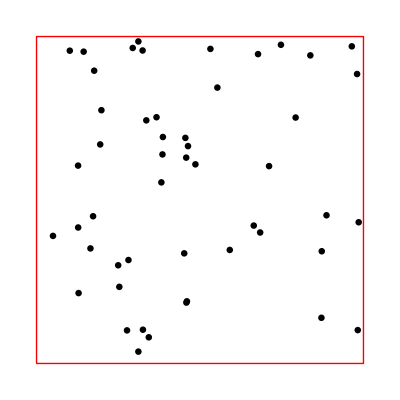

```mathematica
displayParticles[positions, radii, 1]
```

## Analysis

### packingFraction

```mathematica
packingFraction:=radii.radii Pi (1+rate gtime)^2/size^2
```

### dataStore

```mathematica
dataStore:=(
AppendTo[pf, packingFraction];
	nestpositions = AppendTo[nestpositions, positions];
	nestradii = AppendTo[nestradii, radii];
)
```

# Built Algorithm

Note: Their are still precision issues to be dealt with, which are highly dependent on the initial variable definitions. The algorithm will abort when particles overlap by a modifiable amount, to account for these issues.

## Initialization

Read This!

### Numerical Variable Definition

Modify This!

```mathematica
eventspercycle = 20; (*Events per sphere per cycle*)
n=300; (*Number of Spheres*)
steps=eventspercycle n; (*steps per cycle*)
ipf=.5; (*Initial packing fraction*)
rate=.08; (*Growth rate (relative)*)
mpressure=100; (*max pressure*)
gtime = 0 ;(*global time*)
bratio = .5;
rratio = .9;
size = 1;
steps=eventspercycle n; (*steps per cycle*)
```

### Global Variables

Just press Shift-Enter!

Initializes radii, positions, velocities, nextevents, heap, hash, cellMatrix, cellA, lastupdates in that order.

```mathematica
gtime=0;
radii=rlist[ipf, size, n, bratio, rratio];
nrows=optimalGrid[size, radii⟦1⟧];
positions=createDisks[radii, size];
velocities = velocityInit[size, n];
setInitialEvents[n]
changeBins[nrows]
lastupdates=Table[0, n];
nestpositions={positions};
nestradii={radii};
pf={packingFraction};
```

### Process Variables

Press Shift-Enter when restarting simulation.

```mathematica
nchecks=0;
ntrans=0;
ncollisions = 0;
counter = 0;
totalevents=0;
nevents=0;
```

## Process

Evaluate Here (as well!).

### Cycle

```mathematica
packingFraction
```

0.355393

```mathematica
Do[nevents=0;
(Process[];)//AbsoluteTiming, 10]
```

packing fraction 0.369921

System parameters (nchecks, ntrans, ncollisions): 2253 1907 1841

packing fraction 0.380658

System parameters (nchecks, ntrans, ncollisions): 2705 1758 1985

packing fraction 0.390822

System parameters (nchecks, ntrans, ncollisions): 2418 1591 1991

packing fraction 0.401231

System parameters (nchecks, ntrans, ncollisions): 2414 1600 1986

packing fraction 0.413457

System parameters (nchecks, ntrans, ncollisions): 3145 1733 2379

packing fraction 0.423616

System parameters (nchecks, ntrans, ncollisions): 2499 1450 2051

packing fraction 0.433971

System parameters (nchecks, ntrans, ncollisions): 2515 1418 2067

packing fraction 0.450339

System parameters (nchecks, ntrans, ncollisions): 4346 2158 3471

packing fraction 0.4602

System parameters (nchecks, ntrans, ncollisions): 2627 1225 2148

packing fraction 0.470009

System parameters (nchecks, ntrans, ncollisions): 2668 1135 2197

packing fraction 0.479559

System parameters (nchecks, ntrans, ncollisions): 2662 1146 2192

packing fraction 0.493483

System parameters (nchecks, ntrans, ncollisions): 3956 1514 3093

packing fraction 0.50294

System parameters (nchecks, ntrans, ncollisions): 2762 978 2260

packing fraction 0.512285

System parameters (nchecks, ntrans, ncollisions): 2754 1007 2239

packing fraction 0.521371

System parameters (nchecks, ntrans, ncollisions): 2768 966 2266

packing fraction 0.530585

System parameters (nchecks, ntrans, ncollisions): 2800 926 2274

packing fraction 0.541863

System parameters (nchecks, ntrans, ncollisions): 3838 1110 2933

packing fraction 0.550548

System parameters (nchecks, ntrans, ncollisions): 2830 887 2283

packing fraction 0.55891

System parameters (nchecks, ntrans, ncollisions): 2906 751 2343

packing fraction 0.567145

System parameters (nchecks, ntrans, ncollisions): 2905 741 2354

check event error{0.0126119,125,∞}{0.0126119,125,208}

packing fraction 0.575447

System parameters (nchecks, ntrans, ncollisions): 2904 743 2353

packing fraction 0.583222

System parameters (nchecks, ntrans, ncollisions): 2931 692 2377

packing fraction 0.598849

System parameters (nchecks, ntrans, ncollisions): 5776 1340 4660

packing fraction 0.606328

System parameters (nchecks, ntrans, ncollisions): 2968 633 2399

packing fraction 0.614044

System parameters (nchecks, ntrans, ncollisions): 3003 596 2401

packing fraction 0.621137

System parameters (nchecks, ntrans, ncollisions): 2955 666 2379

packing fraction 0.628005

System parameters (nchecks, ntrans, ncollisions): 2982 630 2388

packing fraction 0.635085

System parameters (nchecks, ntrans, ncollisions): 3013 552 2435

packing fraction 0.64155

System parameters (nchecks, ntrans, ncollisions): 2994 605 2401

packing fraction 0.647932

System parameters (nchecks, ntrans, ncollisions): 2991 604 2405

packing fraction 0.654228

System parameters (nchecks, ntrans, ncollisions): 3029 531 2440

packing fraction 0.664309

System parameters (nchecks, ntrans, ncollisions): 5148 847 4024

packing fraction 0.670322

System parameters (nchecks, ntrans, ncollisions): 3067 480 2453

packing fraction 0.67619

System parameters (nchecks, ntrans, ncollisions): 3043 541 2416

check event error{0.00508514,31,∞}{0.00508514,31,25}

packing fraction 0.681846

System parameters (nchecks, ntrans, ncollisions): 3078 485 2437

packing fraction 0.68743

System parameters (nchecks, ntrans, ncollisions): 3085 455 2460

check event error{0.0100165,94,∞}{0.0100165,94,267}

packing fraction 0.692802

System parameters (nchecks, ntrans, ncollisions): 3083 478 2439

check event error{0.0010656,189,∞}{0.0010656,189,21}

packing fraction 0.697995

System parameters (nchecks, ntrans, ncollisions): 3115 427 2458

check event error{0.00444451,283,∞}{0.00444451,283,176}

packing fraction 0.703062

System parameters (nchecks, ntrans, ncollisions): 3088 444 2468

packing fraction 0.707885

System parameters (nchecks, ntrans, ncollisions): 3067 496 2437

packing fraction 0.712725

System parameters (nchecks, ntrans, ncollisions): 3093 443 2464

packing fraction 0.717359

System parameters (nchecks, ntrans, ncollisions): 3094 471 2435

packing fraction 0.722091

System parameters (nchecks, ntrans, ncollisions): 3100 455 2445

packing fraction 0.726802

System parameters (nchecks, ntrans, ncollisions): 3087 449 2464

packing fraction 0.731229

System parameters (nchecks, ntrans, ncollisions): 3117 402 2481

packing fraction 0.735582

System parameters (nchecks, ntrans, ncollisions): 3106 444 2450

packing fraction 0.742004

System parameters (nchecks, ntrans, ncollisions): 4932 674 3775

packing fraction 0.746102

System parameters (nchecks, ntrans, ncollisions): 3120 408 2472

packing fraction 0.750022

System parameters (nchecks, ntrans, ncollisions): 3147 369 2484

check event error{0.00482832,145,∞}{0.00482832,145,28}

packing fraction 0.753764

System parameters (nchecks, ntrans, ncollisions): 3169 357 2474

packing fraction 0.757392

System parameters (nchecks, ntrans, ncollisions): 3148 385 2467

check event error{0.00134524,287,∞}{0.00134524,287,164}

packing fraction 0.760799

System parameters (nchecks, ntrans, ncollisions): 3132 400 2468

check event error{0.00391324,149,∞}{0.00391324,149,239}

check event error{0.00418745,153,∞}{0.00418745,153,165}

packing fraction 0.764276

System parameters (nchecks, ntrans, ncollisions): 3132 406 2462

packing fraction 0.767425

System parameters (nchecks, ntrans, ncollisions): 3156 369 2475

packing fraction 0.770511

System parameters (nchecks, ntrans, ncollisions): 3149 365 2486

packing fraction 0.773421

System parameters (nchecks, ntrans, ncollisions): 3148 355 2497

packing fraction 0.776276

System parameters (nchecks, ntrans, ncollisions): 3147 365 2488

packing fraction 0.778955

System parameters (nchecks, ntrans, ncollisions): 3150 355 2495

packing fraction 0.781503

System parameters (nchecks, ntrans, ncollisions): 3185 317 2498

packing fraction 0.783942

System parameters (nchecks, ntrans, ncollisions): 3186 297 2517

packing fraction 0.786266

System parameters (nchecks, ntrans, ncollisions): 3170 325 2505

packing fraction 0.788537

System parameters (nchecks, ntrans, ncollisions): 3174 334 2492

check event error{0.00247433,50,∞}{0.00247433,50,173}

packing fraction 0.79062

System parameters (nchecks, ntrans, ncollisions): 3156 336 2508

packing fraction 0.79269

System parameters (nchecks, ntrans, ncollisions): 3170 316 2514

packing fraction 0.794659

System parameters (nchecks, ntrans, ncollisions): 3154 337 2509

packing fraction 0.796502

System parameters (nchecks, ntrans, ncollisions): 3183 303 2514

packing fraction 0.798271

System parameters (nchecks, ntrans, ncollisions): 3151 342 2507

check event error{0.0015614,88,∞}{0.0015614,88,210}

packing fraction 0.799908

System parameters (nchecks, ntrans, ncollisions): 3186 305 2509

packing fraction 0.801475

System parameters (nchecks, ntrans, ncollisions): 3175 290 2535

packing fraction 0.802963

System parameters (nchecks, ntrans, ncollisions): 3170 323 2507

packing fraction 0.804413

System parameters (nchecks, ntrans, ncollisions): 3179 298 2523

packing fraction 0.805769

System parameters (nchecks, ntrans, ncollisions): 3181 305 2514

check event error{0.00103521,7,∞}{0.00103521,7,135}

packing fraction 0.807061

System parameters (nchecks, ntrans, ncollisions): 3189 297 2514

packing fraction 0.808251

System parameters (nchecks, ntrans, ncollisions): 3184 274 2542

check event error{0.000797913,178,∞}{0.000797913,178,78}

packing fraction 0.809449

System parameters (nchecks, ntrans, ncollisions): 3159 321 2520

check event error{0.00344663,129,∞}{0.00344663,129,52}

packing fraction 0.810524

System parameters (nchecks, ntrans, ncollisions): 3188 260 2552

check event error{0.00615984,134,∞}{0.00615984,134,190}

packing fraction 0.811565

System parameters (nchecks, ntrans, ncollisions): 3177 290 2533

check event error{0.0033105,190,∞}{0.0033105,190,134}

packing fraction 0.812581

System parameters (nchecks, ntrans, ncollisions): 3189 280 2531

check event error{0.000933323,242,∞}{0.000933323,242,178}

check event error{0.001304,171,∞}{0.001304,171,276}

check event error{0.00206983,176,∞}{0.00206983,176,38}

spheres are already overlapping -0.0000127287

spheres are already overlapping -0.0000236014

spheres are already overlapping -0.0000457531

spheres are already overlapping -0.0000580446

packing fraction 0.813467

System parameters (nchecks, ntrans, ncollisions): 3187 257 2556

spheres are already overlapping -0.0000837799

spheres are already overlapping -0.0000837799

spheres are already overlapping -0.000118534

spheres are already overlapping -0.000132682

spheres are already overlapping -0.000140015

spheres are already overlapping -0.000166053

spheres are already overlapping -0.000290344

spheres are already overlapping -0.000388074

spheres are already overlapping -0.000392537

spheres are already overlapping -0.000511797

After 0 events, overlap.

$Aborted

```mathematica
positions=positions+velocities(gtime-lastupdates);
```

```mathematica
radii=radii(1+gtime rate);
```

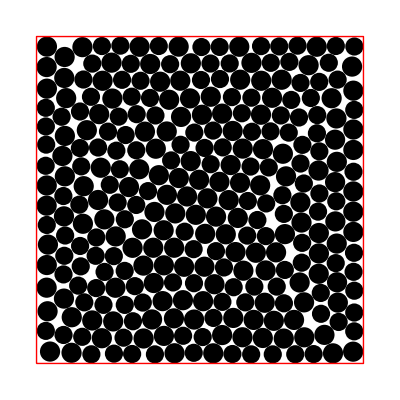

```mathematica
displayParticles[positions, radii, size]
```

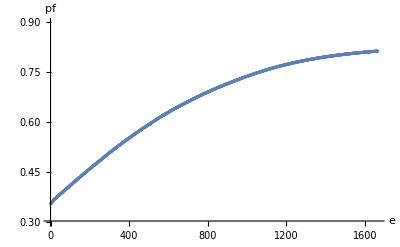

```mathematica
ListPlot[pf, AxesLabel->{"e", "pf"}, PlotRange->{Automatic, {.3, .9}}]
```

```mathematica
Do[nevents=0;
(Process[];)//AbsoluteTiming, 10]
```

```mathematica
Module[{np=nestpositions, nr=nestradii},
Manipulate[displayParticles[np⟦i⟧, nr⟦i⟧, size], {i, 1, np//Length, 1}]
]
```

# Visualizations

Each plot will be parametrized by a list {rratio, bratio, n}.

### (.5, .5, 300)

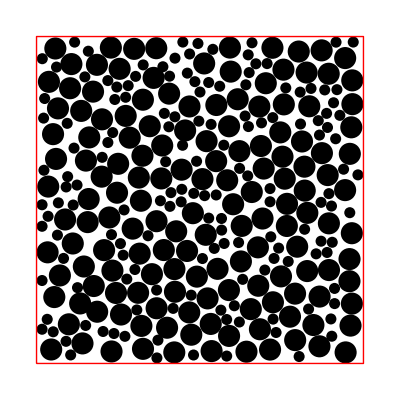

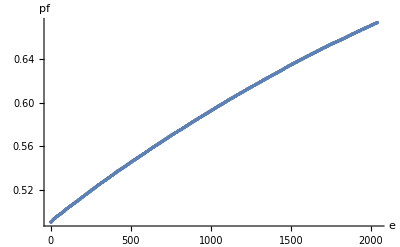

### (.9, .5, 300)

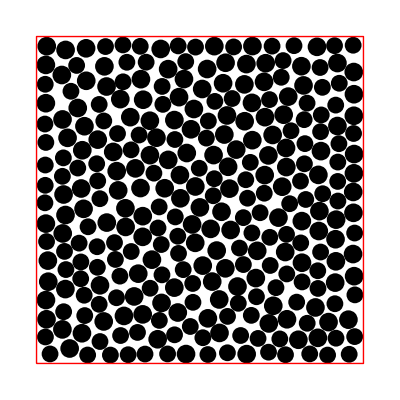

```mathematica
data=Import["C:\\Users\\rab\\Documents\\data"];
```

```mathematica
nestp=data⟦1⟧;
nestr=data⟦2⟧;
```

```mathematica
nestp⟦1⟧;
```

### (.6, .5, 300)

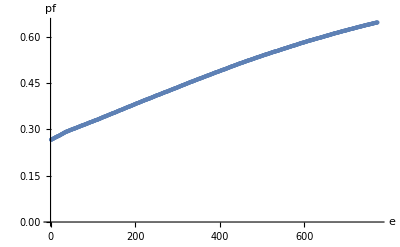

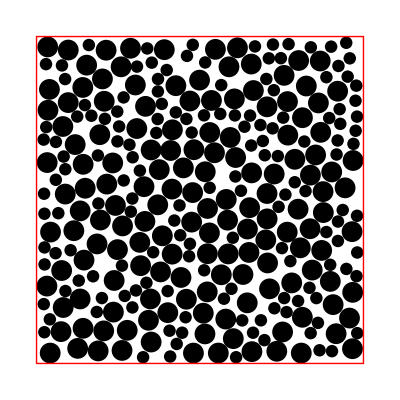

# Keywords

Material Science

Molecular Dynamics

MinHeap

# References

“Packing hard spheres in high dimensional Euclidean spaces”, by M. Skoge, A. Donev, F. H. Stillinger, and S. Torquato, Phys. Rev. E, Vol. 74: 041127 (2006) [ibid 75: 029901 (2007)], [cond-mat/0608362]

https://arxiv.org/ftp/physics/papers/0405/0405089.pdf neighbor list collision-driven molecular dynamics simulation for nonspherical hard particles

F. H. Stillinger and B. D. Lubachevsky, Crystalline-Amorphous Interface Packings for Disks and Spheres, J. Stat. Phys. 73, 497-514 (1993)

http://pi.math.cornell.edu/~connelly/ bobs page

https://link.springer.com/content/pdf/10.1007%2Fs00454-005-1172-4.pdf compact packings of the plane

https://link.springer.com/content/pdf/10.1007%2Fs00454-003-0007-6.pdf some densest 2-size disc packings in the plane

https://arxiv.org/ftp/cond-mat/papers/0608/0608334.pdf Hypoconstrained jammed packings of Nonspherical Hard Particles: Ellipses and Ellipsoids